```mathematica
ContourPlot3D[{ (qx^2+qy^2+qz^2)^2==1, (qx^2+qy^2)+(qx^2+qy^2+qz^2)^2==1},{qx,-1,1},{qy,-1,1},{qz,-1,1},Mesh->None,PlotRange->{{-1,1},{-1,1},{-1,1}},ContourStyle->{Directive[Blue,Opacity[0.3],Specularity[White,30]],Directive[Green,Opacity[0.4],Specularity[White,30]]},
Ticks->{{{-1,Style["-√(ω/v)",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontColor->Black]},{0,0},{1,Style["√(ω/v)",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontColor->Black]}},{{-1,Style["-√(ω/v)",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontColor->Black]},{0,0},{1,Style["√(ω/v)",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontColor->Black]}},{{-1,Style["-√(ω/v)",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontColor->Black]},{0,0},{1,Style["√(ω/v)",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontColor->Black]}}},
TicksStyle-> Directive[FontSize-> 25,FontFamily -> "Latin Modern Roman",FontColor->Black],
AxesStyle->Directive[Black,Thickness[0.005]],
AxesLabel->{Style["q_y",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->40,FontColor->Black],Style["q_x",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->40,FontColor->Black],Style["q_z",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->40,FontColor->Black]},
PlotLabel->Style["(a) ",FontSlant->Plain,FontFamily -> "Latin Modern Roman",FontSize->40,FontColor->Black],ViewPoint->{1.2, -2.4, 1.2},ImagePadding->{{Scaled[0.08],Scaled[0.08]},{Scaled[0.08],Scaled[0.08]}},ImageSize->500,BoxRatios->{1, 1, 1}]
```

-Graphics3D-

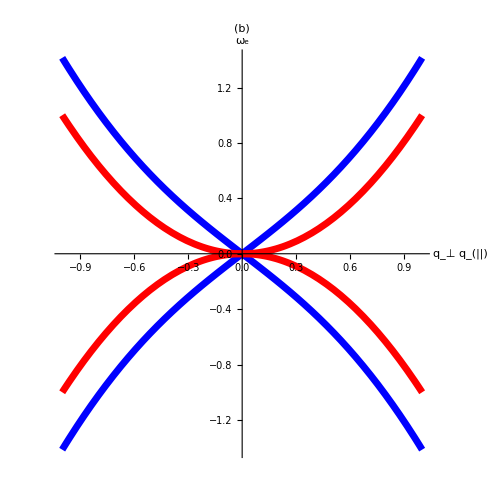

```mathematica
Plot[{√(qx^2+ (qx^2)^2),-√(qx^2+ (qx^2)^2),√((qx^2)^2),-√((qx^2)^2)},{qx,-1,1},PlotStyle->{{Thickness[0.01],Blue},{Thickness[0.01],Blue},{Thickness[0.01],Red},{Thickness[0.01],Red}},
TicksStyle-> Directive[FontSize-> 25,FontFamily -> "Latin Modern Roman",FontColor->Black],
AxesStyle->Directive[Black,Thickness[0.005]],AxesLabel->{Column[{Style["q_⊥",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->40,FontColor->Blue],Style["q_(||)",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->40,FontColor->Red]}],Style["ω_e",FontSlant->Italic,FontFamily -> "Latin Modern Roman",FontSize->40,FontColor->Black]},PlotLabel->Style["(b) ",FontSlant->Plain,FontFamily -> "Latin Modern Roman",FontSize->40,FontColor->Black],ImagePadding->{{Scaled[0.08],Scaled[0.08]},{Scaled[0.08],Scaled[0.08]}},ImageSize->500,AspectRatio->1]
```

```mathematica
Plot3D[{√(2 c2 qx^2+v^2 (qx^2+qz^2)^2),-√(2 c2 qx^2+v^2 (qx^2+qz^2)^2),v^2 (qx^2+qz^2)^2,-v^2 (qx^2+qz^2)^2},{qx,-1,1},{qz,-1,1},PlotRange->{-1,1},ClippingStyle->None,BoxRatios->{1, 1, 1},PlotStyle->{{RGBColor[255/255,0/255,0/255],Opacity[0.75]},{RGBColor[255/255,0/255,0/255],Opacity[0.75]},{RGBColor[255/255,0/255,0/255],Opacity[0.25]},{RGBColor[255/255,0/255,0/255],Opacity[0.25]}},Mesh->None,ViewPoint->{2, 2, 0.1},ImageSize->500,Axes->False,Boxed->False,Lighting->{"Ambient",White,{0.4, 8, 0.6}}]
```

-Graphics3D-

```mathematica
|
```

$Failed

Syntax::sntxi: Incomplete expression; more input is needed.

ToExpression::esntx: Could not parse BoxData[|] as input.